# Velocity distribution in an ideal gas

#### G. Woehlke, Jan. 2022-2026

```mathematica
Button["Go to section Distance calculator",NotebookLocate[{"MathCode_01_MaxwellDistribution.nb","calculator"}],Background->LightYellow]
```

Go to section Distance calculator

## 1. Maxwell velocity distribution in H_2, He, N_2, O_2, and Ar under ideal conditions

We pull a list of elements from Wolfram:

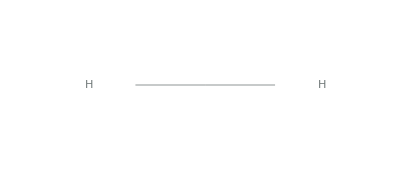
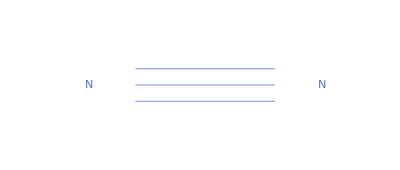
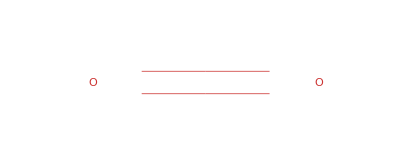
Molecule | Molecular Mass
-Graphics- | 2.016 u
-Graphics- | 4.002602 u
-Graphics- | 28.014 u
-Graphics- | 31.998 u
-Graphics- | 39.948 u

```mathematica
{{"Molecule","Molecular Mass"},{ChemicalData["Hydrogen"],ChemicalData["Hydrogen","MolecularMass"]},
{ChemicalData["Helium"],ChemicalData["Helium","MolecularMass"]},
{ChemicalData["Nitrogen"],ChemicalData["Nitrogen","MolecularMass"]},
{ChemicalData["Oxygen"],ChemicalData["Oxygen","MolecularMass"]},
{ChemicalData["Argon"],ChemicalData["Argon","MolecularMass"]}}//TableForm
```

We plot the velocity distribution. Comments to the code: The function MaxwellDistribution[σv] is defined such that the energy is scaled in relation to σv, and equals √((2 k_B T)/m). This parameter defines the distribution 𝒟. Note that the maximum of the distribution is  (the most likely velocity), whereas the mean velocity (where half of the particles are slower, half are faster) is .
The function PDF[ ] stands for “point density function”, i.e. the frequency of events that the velocity on the x axis. Other elements of the code are used for styling and formatting.

Reference: Mathematica documentation of MaxwellDistribution[ ].

```mathematica
Manipulate[σv=Block[{k=Quantity["BoltzmannConstant"],t=Quantity[T,"Kelvins"]},√(k t/m)]//UnitConvert;𝒟=MaxwellDistribution[σv];
Plot[PDF[𝒟,Quantity[v,"Meters"/"Seconds"]]//Evaluate,{v,0,6500},PlotRange->{Full,{0,Full}},Filling->filling,AxesLabel->{"m/s","densisty function"},PlotLabel->"Velocity distribution",PlotStyle->{color,Thickness[thn]},LabelStyle->fs,ImageSize->is,Epilog->{PointSize[0.02],Point[{QuantityMagnitude[UnitConvert[Mean[𝒟]]],0}],Inset[Style[StringJoin["Temperature ",ToString[T]," K = ",ToString[T-273.]," °C","\rMean velocity ",ToString[Mean[𝒟]//UnitConvert]],fs,TextAlignment->Left],{5000,Center}]}],
{color,{Blue,RGBColor[0.5,0.5,0.85],Black,Darker[Gray],Orange,Red,Darker[Green]}},
{{filling,Axis},{None,Axis}},
{{fs,21,"Font size"},{14,18,21,24,28}},
{{thn,0.005,"Line thickness"},0.001,0.025},
{{is,720,"Image size"},{450,650,720,950,1050,1280}},
{{T,293.,"Temperature/K"},150,1200,Appearance->"Open"},{m,{ChemicalData[Entity["Element","Hydrogen"],"MolecularMass"]->"H_2",ChemicalData[Entity["Element","Helium"],"MolecularMass"]->"He",
ChemicalData[Entity["Element","Nitrogen"],"MolecularMass"]->"N_2",ChemicalData[Entity["Element","Oxygen"],"MolecularMass"]->"O_2",ChemicalData[Entity["Element","Argon"],"MolecularMass"]->"Ar"},ControlType->PopupMenu}
]
```

## 2. Molar volume, mean particle distance, and internal energy

```mathematica
CellPrint[TextCell["Simple calculator",CellTags->"calculator","Subsection"]]
```

### Simple calculator

Together with the theory of ideal gases, we can estimate the volume of a certain amount of gas (in moles) at given temperature and pressure. We can further calculate ⟨Δs⟩, the mean distance of gas atoms (or molecules; ((n_A N)/V)^(1/3)), and the kinetic energy of the atoms/molecules (3/2 k_BT for three degrees of freedom).
The collision frequency may be calculated from mean velocity and mean distance (⟨v⟩/⟨Δs⟩ = 1/Δt). 
One may intuitively suspect that two particles that fly towards each other encounter at half the mean distance. However, the flight direction with respect to the connecting line between their positions is random. Both particles may move in the same direction (albeit with different velocities) such that the actual travelling distance Δd until the encounter will be much larger than the mean ⟨Δs⟩. The directional component towards each other will be compensated by the component away from each other.

```mathematica
Manipulate[nA=Quantity[6.02214199×10^23,1/"Moles"];kB=Quantity[1.380649 10^-23,"Joules"/"Kelvins"];
TableForm[
{{"Temperature °C","T_(°C) = T-273.15 K",
UnitConvert[
Quantity[T,"Kelvins"],"DegreesCelsius"]},
{"Volume","V = n×R×T/p",
UnitConvert[
Quantity[amt,"Moles"] nA kB Quantity[T,"Kelvins"]/Quantity[p,"Millibars"],
"Liters"]},
{"Particle distance ⟨Δs⟩","(n_A/V)^(1/3)",
UnitConvert[((kB Quantity[T,"Kelvins"])/Quantity[p,"Millibars"])^(1/3),"Nanometers"]},
{"Particle's kinetic energy","3/2k_BT",
UnitConvert[(3 kB)/2 Quantity[T,"Kelvins"],"Joules"]},
{"Mean velocity","√((8 SubscriptBox[k, B] T)/(π m))",
UnitConvert[√((8 kB Quantity[T,"Kelvins"])/(π m)) ]},
{"Mean collision frequency","⟨v⟩/⟨Δs⟩",
UnitConvert[2 √(2/π) (Quantity[p,"Millibars"]/(Quantity[T,"Kelvins"] kB))^(1/3) √((Quantity[T,"Kelvins"] kB)/m) ]}},
TableHeadings->{None,{"Parameter","Calculation","Value"}}
],
{{m,ChemicalData[Entity["Element","Helium"],"MolecularMass"],"Element"},{ChemicalData[Entity["Element","Hydrogen"],"MolecularMass"]->"H_2",ChemicalData[Entity["Element","Helium"],"MolecularMass"]->"He",
ChemicalData[Entity["Element","Nitrogen"],"MolecularMass"]->"N_2",ChemicalData[Entity["Element","Oxygen"],"MolecularMass"]->"O_2",ChemicalData[Entity["Element","Argon"],"MolecularMass"]->"Ar"},ControlType->PopupMenu},{{amt,1.,"Amount/moles"},0.1,10,Appearance->"Open"},
{{T,273.15,"Temperature/K"},50.,800.,Appearance->"Open"},
{{p,1013.,"Pressure/mBar"},100,10000,Appearance->"Open"}]
```

/Users/guenther_work/Lehre_TUM/VL-Biochem_Media/Thermodynamik/MaxwellDistribution_20220121.nb

```mathematica
NotebookInformation[]
```

{FileName→FrontEnd`FileName[{$RootDirectory,Users,guenther_work,Publication,MolecularMachines_Springer_2025,MathematicaCode},MathCode_01_MaxwellDistribution.nb,CharacterEncoding→UTF-8],FileModificationTime→3.98351×10^9,WindowTitle→MathCode_01_MaxwellDistribution.nb,MemoryModificationTime→3.98351×10^9,ModifiedInMemory→True,StorageSystem→Local,DocumentType→Notebook,MIMEType→application/vnd.wolfram.nb,StyleDefinitions→{},ExpressionUUID→f3d1bf1c-aa86-4a4d-bf66-174ce3c11426}